# Setup

Learn the color codes:
Gray: optional cells (except for the one cell right below: this installs and preloads some needed data and must be run every time the notebook is used in a new computer)
Yellow: initialization cells: these must be run to load all the data
Purple: cells that print out some stuff that I did not include in my paper
Green: cells that generate graphs I used in my paper. Most green cells can be run without having run other cells prior. If there are two consecutive green cells without output, it might mean that the first cell generates something and the second cell plots it).
Red: unfinished cells

```mathematica
CityData[All,"Preload"];
RebuildPacletData[];
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

```mathematica
data = Import[NotebookDirectory[]<>"../data/trainline/network.csv", "CSV"];
data = Flatten[{#, N[#[[4]]/#[[3]]]}]&/@data;
max = Max[data[[;;, 9]]];
data = Flatten[{#,(#[[9]]/max)^.2}]&/@data;
data // Dataset
```

```mathematica
g = Graph[#1 <->#2 &@@@ data, VertexLabels->None];
geoLocationGraph=GeoPosition[{#5,#6}]<->GeoPosition[{#7,#8}]&@@@data;

nameIndex = SortBy[DeleteDuplicates[Flatten@Transpose[data][[1;;2]]],-QuantityMagnitude[CityData[#,"Population"],"People"]&];
getCoords = (name) |->data[[Position[data, name][[1, 1]], 5;;6]];

getIndex=(name)|->Position[nameIndex,name][[1, 1]];

wmat=Table[0,{x,1,VertexCount@g},{y,1,VertexCount@g}];
inverseWmat=Table[0,{x,1,VertexCount@g},{y,1,VertexCount@g}];
(wmat[[getIndex[#1],getIndex[#2]]]=#3/#4)&@@@data;
(inverseWmat[[getIndex[#1],getIndex[#2]]]=#4/#3)&@@@data;

wg=WeightedAdjacencyGraph[wmat,DirectedEdges->True];
(*g=AdjacencyGraph[Ceiling[Symmetrize[wmat],1]]*)
```

# Plot adjacency matrix

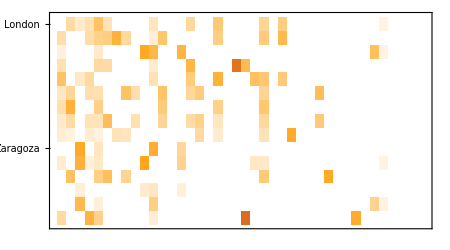

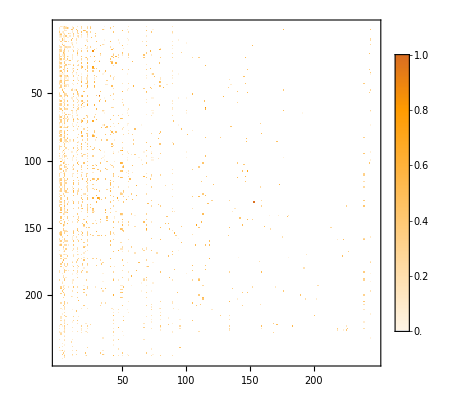

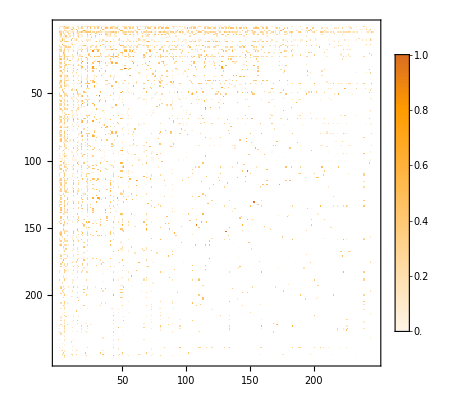

```mathematica
rowticks = Thread[{Range@Length@nameIndex,nameIndex}];
colticks = Thread[{Range@Length@nameIndex,Rotate[#, 90 Degree]&/@nameIndex}];

asymmPlot = MatrixPlot[(Rescale@inverseWmat)[[;;15,;;40]], MaxPlotPoints->Infinity,PlotTheme->{"Scientific", "Web"},ImageSize->{450, 250}, FrameTicks->{rowticks, None, None, colticks}]
asymmFull = MatrixPlot[Rescale@inverseWmat, MaxPlotPoints->Infinity,PlotTheme->{ "Detailed", "Scientific", "Web"}]
symmFull = MatrixPlot[Rescale@Symmetrize[inverseWmat], MaxPlotPoints->Infinity, PlotTheme->{ "Detailed", "Scientific", "Web"}]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/asymmPlotHalf.pdf",asymmPlot]
Export[NotebookDirectory[]<>"../assets/asymmPlotFull.pdf",asymmFull]
Export[NotebookDirectory[]<>"../assets/symmPlotFull.pdf",symmFull]
```

D:\complex-networks\src\../assets/asymmPlotHalf.pdf

D:\complex-networks\src\../assets/asymmPlotFull.pdf

D:\complex-networks\src\../assets/symmPlotFull.pdf

# Plot some nice visualizations

```mathematica
GraphPlot[g] // rasterTrick
(*GraphPlot[wg]; useless *)
GeoGraphPlot[geoLocationGraph, PerformanceGoal->"Speed", RasterSize->1000]
```

-Graphics-

-Graphics-

```mathematica
nodes = VertexList[geoLocationGraph];
degree = VertexDegree[geoLocationGraph];
degreeChart = GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Quality", RasterSize->1000, ColorFunction->"RustTones",GeoBackground->"VectorMonochrome", ImageSize->Large];
rasterDegreePlot = Rasterize[degreeChart, RasterSize->4000, ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/degreePlot.pdf",rasterDegreePlot]
```

D:\complex-networks\src\../assets/degreePlot.pdf

```mathematica
(*^^ Map is in something projection, the balls are not*)
```

```mathematica
getBezier[x_, y_]:=({GeoPosition@x, GeoPosition[(x+y)/2+Cross[x-y]/8], GeoPosition@y})
getCity = (coords) ↦ GeoNearest["City", coords][[1]] ;
data = Sort[data,#1[[10]]<#2[[10]]&];
i = 0;
ProgressIndicator[Dynamic[i/Length[data]]]
bigPlot = GeoGraphics[
{
(i++;{
Thickness[.002],
 Arrowheads[{{0.01,0.6,{Graphics[{Opacity[1],  Hue[.65,#10, 1],,Polygon[{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]}],0}}}],
 Hue[.65,#10, 1],
Opacity[1],
{Opacity[1],PointSize[.007],Black, Point[VertexList[geoLocationGraph]]},
{Opacity[1],PointSize[.005],Cyan, Point[VertexList[geoLocationGraph]]},
Arrow[
BezierCurve[
getBezier[{#5,#6},{#7,#8}]]
]})&@@@data
},
GeoScaleBar->"Metric", GeoProjection->"Orthographic", GeoGridLines->Automatic, GeoBackground->"VectorMonochrome",  ImageSize->{1414, 1000}
];
rasterBigPlot = Rasterize[bigPlot, RasterSize->4000, ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/rasterBigPlot.pdf",rasterBigPlot]
```

D:\complex-networks\src\../assets/rasterBigPlot.pdf

# Check for scale free network

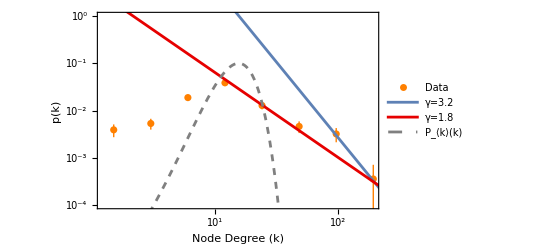

```mathematica
vertexDegreeList = VertexDegree@g;
binWidth = PowerRange[1, 600, 2];
hist = Histogram[vertexDegreeList, {binWidth}];
dataNoErrors = Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
normFactor =Total[Differences[PowerRange[1, 500, 2]].dataNoErrors[[;;,2]]];
datafromrectangles=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]/normFactor ± Sqrt[b[[2]]]/normFactor },All];


gamma =3.2;
kmin = 38;
norm = 1/Zeta[gamma];
fit[x_] :=(gamma-1) kmin^(gamma-1)  x^(-gamma)

degreePlotLogLog = Show[
ListPlot[datafromrectangles,PlotStyle->Orange,PlotRange->{Full, {10^(-4), 1}},PlotTheme->{"FrameGrid"}, ScalingFunctions->{"Log10", "Log10"}, FrameLabel->{"Node Degree (k)", "p(k)"}, LabelStyle->{Black, 12}, PlotLegends->{"Data"}],
Plot[fit[x],{x,-50,1000},PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}, PlotLegends->{"γ=3.2"}],
Plot[4x^(-1.8),{x,-50,1000},PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{ Hue[1,1,0.9]}, PlotLegends->{"γ=1.8"}],
Plot[PDF[PoissonDistribution[Mean@vertexDegreeList], x] // Evaluate, {x, 1, 200}, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{Gray, Dashed}, PlotLegends->{"P_⟨k⟩(k)"}]
(*Graphics[{Black,Rectangle[{3.91,4.42},{4.54,5.98}]}],
Graphics[{White,Rectangle[{3.925,4.5},{4.525,5.9}]}],Graphics[Text[Style["\!\(\*SuperscriptBox[OverscriptBox[\(χ\), \(_\)], \(2\)]\)=1.05",FontSize->16,FontFamily->"Courier"],{4.22,5.2}]]*)
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/degreePlotLogLog.pdf",degreePlotLogLog]
```

D:\complex-networks\src\../assets/degreePlotLogLog.pdf

FittedModel[…]

3.66349

2.42446

2.23

2.27619

1.70645

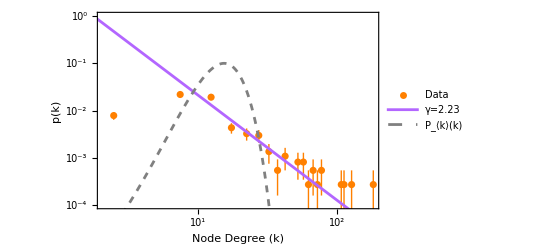

```mathematica
vertexDegreeList = VertexDegree@g;
binWidth = 15;
bins = Table[x, {x, 300, binWidth}];
hist = Histogram[vertexDegreeList, {bins}];
dataNoErrors = Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
normFactor =Length[vertexDegreeList]*binWidth;
datafromrectangles=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]/normFactor ± Sqrt[b[[2]]]/normFactor},All];


data2=Log10@Transpose[(dataNoErrors[[3;;-10]] // Transpose)/{1, normFactor}];
lm=LinearModelFit[data2,x,x]
estimates=lm["BestFitParameters"];

gamma =-estimates[[2]];
norm = 10^estimates[[1]]
kmin = (norm/(gamma-1))^(1/(gamma-1))
gamma = SetPrecision[gamma, 3]
MeanGraphDistance@g //N
Log[Log[VertexCount@g]] //N

(*
pearsonTest[obs_List,exp_List]/;Length[obs]==Length[exp]:=Block[{t},t=Total[(obs-exp)^2/exp]//N;
{Rule["chisqr",t],Rule["p-val",SurvivalFunction[ChiSquareDistribution[Length[exp]-1],t]]}]

(*Adjust by hand points on which chi2 is computed*)
testPoints = ((Differences[PowerRange[1, 1200, 2]] / 2) + binWidth)[[;;-3]];
saturationCutoff = 4;
test = pearsonTest[dataNoErrors[[saturationCutoff;;]], Table[{x, fit[x]},{x, testPoints}][[saturationCutoff;;]]]
chisqr = ("chisqr" /. test);
If[chisqr[[1]]!= 0, Print["SOMETHING IS WRONG WITH THE BINS!"]]
chisqrReduced = chisqr[[2]] / (Length[testPoints]-2)
*)

degreePlotLogLogLinspace = Show[
ListPlot[datafromrectangles,PlotStyle->Orange,PlotRange->{Full, {10^(-4), 1}},PlotTheme->{"FrameGrid"}, ScalingFunctions->{"Log10", "Log10"}, FrameLabel->{"Node Degree (k)", "p(k)"}, LabelStyle->{Black, 12}, PlotLegends->{"Data"}],
Plot[10^estimates[[1]]x^estimates[[2]],{x,-50,1000},PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}, PlotLegends->{"γ=2.23"},PlotStyle->{Hue[0.75,0.6,1]}],
Plot[PDF[PoissonDistribution[Mean@vertexDegreeList], x] // Evaluate, {x, 1, 200}, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{Gray, Dashed}, PlotLegends->{"P_⟨k⟩(k)"}]
(*Graphics[{Black,Rectangle[{3.91,4.42},{4.54,5.98}]}],
Graphics[{White,Rectangle[{3.925,4.5},{4.525,5.9}]}],Graphics[Text[Style["\!\(\*SuperscriptBox[OverscriptBox[\(χ\), \(_\)], \(2\)]\)=1.05",FontSize->16,FontFamily->"Courier"],{4.22,5.2}]]*)
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/degreePlotLinSpace.pdf",degreePlotLogLogLinspace]
```

D:\complex-networks\src\../assets/degreePlotLinSpace.pdf

```mathematica
Log[247]/(Log[Log[247]]) //N
```

3.22856

# Test properties when small nodes are deleted

```mathematica
threshold = 1000000;
i = 0;
ProgressIndicator[Dynamic[i / VertexCount[geoLocationGraph]]]
g1 = VertexDelete[geoLocationGraph, coords_/;(i++; GeoNearest["AdministrativeDivision", coords][[-1]]["Population"] < threshold)];
nodes = VertexList[g1];
degree = DegreeCentrality[g1];
GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Speed", RasterSize->1000, PlotTheme->"Business", GeoBackground->"VectorMonochrome", ImageSize->Large]
```

# Communities

```mathematica
nodes = VertexList[geoLocationGraph];
degrees = BetweennessCentrality[geoLocationGraph];
communitiesPlot = GeoBubbleChart[{nodes, degrees} // Transpose, PerformanceGoal->"Speed", RasterSize->1000, ChartStyle->Orange, GeoBackground->"VectorMonochrome", ImageSize->Large, ColorFunction->"SolarColors"];
rasterCommPlot = Rasterize[communitiesPlot, RasterSize->4000, ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/communitiesPlot.pdf",rasterCommPlot]
```

D:\complex-networks\src\../assets/communitiesPlot.pdf

```mathematica
(*CommunityGraphPlot[g, FindGraphCommunities[g, Method->"Centrality"] ,Method->"Hierarchical",VertexLabels->"Name", PlotTheme->{"Large", "Classic"}, PlotLegends->Automatic]*)
communities = FindGraphCommunities[geoLocationGraph,  Method->"Hierarchical"];
subgraphs = Subgraph[geoLocationGraph,#]&/@communities;
colors = Flatten[{{Red, Cyan, Yellow, Green}, Table[White, {i, 1, Length@communities - 4}]}];
communitiesRainbow = GeoGraphics[
{
{Black, PointSize[.015],Point[#]} &/@ communities,
{#1, PointSize[.012],Point[#2]} &@@@ Transpose[{colors, communities}]
},
GeoScaleBar->"Metric", RasterSize->1000, GeoProjection->"Orthographic",GeoGridLines->Automatic, GeoBackground->"VectorMonochrome", ImageSize->Large
];
commRainbowRaster=Rasterize[communitiesRainbow,RasterSize->4000,ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/communitiesRainbow.pdf",commRainbowRaster]
```

D:\complex-networks\src\../assets/communitiesRainbow.pdf

FittedModel[…]

{0.839458,0.268335}

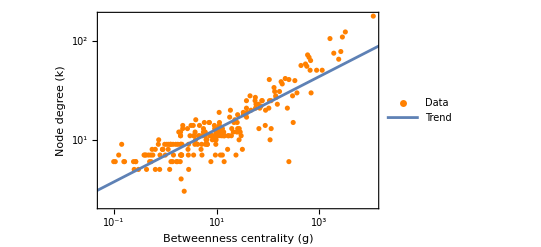

```mathematica
data = {BetweennessCentrality@g, VertexDegree@g} // Transpose ;
lm=LinearModelFit[DeleteCases[Log10[data], {Indeterminate, _}, 2], x, x]
estimates=lm["BestFitParameters"]
centralityDegreeCorrelation = Show[
ListPlot[data, PlotTheme->{"FrameGrid"},  PlotLegends->{"Data"},FrameLabel->{"Betweenness centrality (g)", "Node degree (k)"}, LabelStyle->{Black, 12}, PlotStyle->Orange, PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}],
Plot[lm[x], {x, -2, 5}, PlotLegends->{"Trend"}]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/centralityDegreeCorrelation.pdf",centralityDegreeCorrelation]
```

D:\complex-networks\src\../assets/centralityDegreeCorrelation.pdf

# Degree correlations

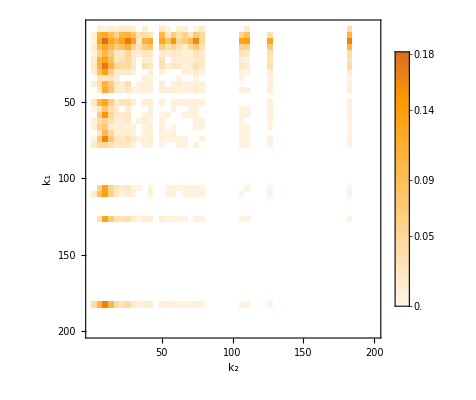

3952

3608

-0.268587

FittedModel[…]

{2.01298,-0.340637}

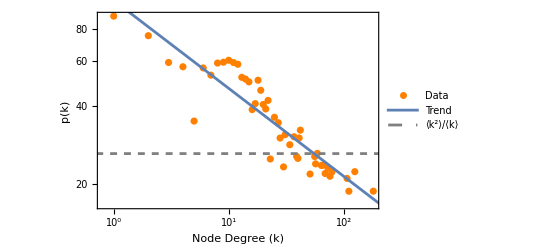

```mathematica
vertexCount = VertexCount@g;
correlationMatrix = Table[Table[0, {y, 0, vertexCount}], {x, 0, vertexCount}];
nodes = Transpose[{VertexList[g], VertexDegree[g]}];
For[i = 1, i <= vertexCount,  i++,
(
currentNode = nodes[[i]];
neighbors = VertexList@NeighborhoodGraph[ g,currentNode[[1]]] ~ DeleteCases ~ currentNode[[1]];
For[j = 1, j<=Length@neighbors, j++,
neighborDegree = VertexDegree[g, neighbors[[j]]];
correlationMatrix[[currentNode[[2]], neighborDegree]]++;
]
)
];
assortativityMatrix = MatrixPlot[Rescale@correlationMatrix , PlotRange->{{0, 200}, {0, 200}},PlotTheme->{ "Detailed", "Scientific", "Web"}, MaxPlotPoints->50, LabelStyle->{Black, 12}, FrameLabel->{"k_1", "k_2"}]
Total[VertexDegree@g]
Total@Total[correlationMatrix]
GraphAssortativity[g] //N

s = Symmetrize[inverseWmat];
knn[node_] :=  Total[  VertexDegree[g,#]&/@VertexList@NeighborhoodGraph[ g,node]] /  VertexDegree[g, node]
correlationPoints = {VertexDegree[g, #],knn[#]}&/@ VertexList[g];
(*Take average of nodes with same degree*)
correlationPoints = Transpose[Through[{Keys,Values}[KeySort@GroupBy[correlationPoints,First->Last,Mean]]]];

data2=Log10[correlationPoints];
lm=LinearModelFit[data2,x,x]
estimates=lm["BestFitParameters"]

 assortativityPlot = Show[
ListPlot[correlationPoints , ScalingFunctions->{"Log10", "Log10"}, PlotTheme->{"FrameGrid"},  PlotLegends->{"Data"},FrameLabel->{"Node Degree (k)", "k_nn(k)"}, LabelStyle->{Black, 12}, PlotStyle->Orange],
Plot[10^(estimates[[1]]+estimates[[2]] Log10[i]), {i, 0, 1000}, ScalingFunctions->{"Log10", "Log10"}, PlotRange->Full, PlotLegends->{"Trend"}],
Plot[Variance[VertexDegree@g]/Mean[VertexDegree@g], {x, .1, 1000}, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{Gray, Dashed}, PlotLegends->{"⟨k^2⟩/⟨k⟩"}]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/assortativityMatrix.pdf",assortativityMatrix]
Export[NotebookDirectory[]<>"../assets/assortativityPlot.pdf",assortativityPlot]
```

D:\complex-networks\src\../assets/assortativityMatrix.pdf

D:\complex-networks\src\../assets/assortativityPlot.pdf

# Actual robustness che funziona

## Random failures

### Molloy-reed criterion

(predicts critical threshold for random failures on scale free network)

```mathematica
degrees = VertexDegree[g];
molloyValue = N@Variance[degrees] / Mean [degrees]
molloyValue > 2

breakdownThreshold = 1-1/(molloyValue-1)
(*TODO su overleaf spiega andamento di breakdownThreshold in funzione di gamma*)

breakdownThresholdRandom = 1 - 1/Mean [degrees] //N
breakdownThreshold > breakdownThresholdRandom (*Enhanced robustness*)
```

26.2779

True

0.96044

0.9375

True

### Simulation

```mathematica
pinf = {};
SetSharedVariable[pinf]
totalNodes = VertexCount[g];
ParallelDo[
	runs = {};
	
	For[run = 0, run < 16, run++,
	tempGraph = g;
	For [i=0, i < nodeRemovedCount, i++,
	tempGraph = VertexDelete[tempGraph,RandomChoice[VertexList[tempGraph]]];
	];
	AppendTo[runs, (Length@Last@Sort@ConnectedComponents@tempGraph)/(totalNodes)];
	];
	
	AppendTo[pinf, {nodeRemovedCount / totalNodes, Mean[runs]±StandardDeviation[runs]}];
, {nodeRemovedCount, 0, totalNodes-1}];
```

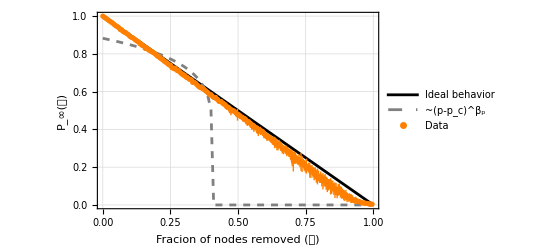

```mathematica
pc = .593; (*Values for 2D square lattice*)
 betap = 5/36;

randomFailuresPlot = Show[
Plot[-x + 1,{x, 0,1 }, PlotStyle->{ Black}, PlotTheme->{"FrameGrid"}, PlotLegends->{"Ideal behavior"}, FrameLabel->{"Fracion of nodes removed (𝑓)", "P_∞(𝑓)"}, LabelStyle->{Black, 12}],
ListLinePlot[Table[{p, HeavisideTheta[-p+(1-pc)](-p+(1-pc))^(betap) // Evaluate}, {p, 0, 1, .01}], PlotStyle->{Gray, Dashed}, PlotLegends->{"~(p-p_c)^β_p"}],
ListPlot[pinf, PlotStyle->Orange, PlotLegends->{"Data"}]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/raindomFailuresPlot.pdf",randomFailuresPlot]
```

D:\complex-networks\src\../assets/raindomFailuresPlot.pdf

## Targeted attack

### Critical threshold for attacks on scale free network

2.8

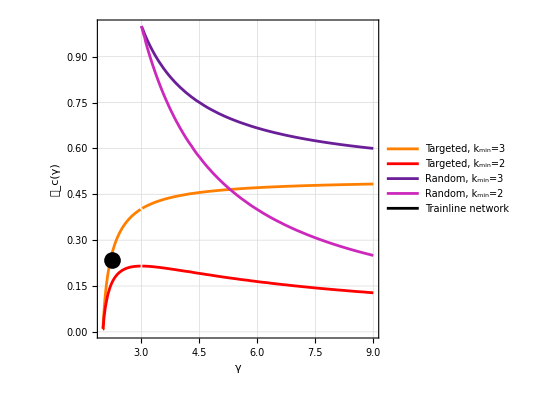

```mathematica
Min[VertexDegree[g]];
kmin=2.8

bigAssEquation[kmin_] := fc^((2-γ)/(1-γ))==2+((2-γ)/(3-γ)) kmin(fc^((3-γ)/(1-γ))-1)
fc[kmin_] := fc == If[γ>3,1-1/(kmin(γ-2)/(γ-3) - 1)]

fcPlot = Show[
ContourPlot[bigAssEquation[3] // Evaluate,  {γ, 2, 9}, {fc, 0, 1}, ContourStyle->{Orange}, PlotTheme->{"FrameGrid"},GridLines->Automatic, FrameLabel->{ "γ", "(|01d453)_c(γ)"}, LabelStyle->{Black, 13}, PlotLegends->{"Targeted, k_min=3"}], (*idk what evaluate does but it fixes the thing*)
ContourPlot[bigAssEquation[2] // Evaluate,  {γ, 2, 9}, {fc, 0, 1}, ContourStyle->{Red}, PlotLegends->{"Targeted, k_min=2"}], 
ContourPlot[fc[3] // Evaluate,  {γ, 1, 9}, {fc, 0, 1}, ContourStyle->{Hue[0.77,0.8,0.6]}, PlotLegends->{"Random, k_min=3"}],
ContourPlot[fc[2] // Evaluate,  {γ, 1, 9}, {fc, 0, 1}, ContourStyle->{Hue[0.85,0.8,0.8]}, PlotLegends->{"Random, k_min=2"}],
Graphics[{ PointSize[.03], Point[{gamma, fc /. NSolve[(bigAssEquation[kmin]/. γ->gamma), fc][[-1]]}]}],
Plot[0, {x, 0, 1}, PlotStyle->{Black},PlotLegends->{"Trainline network"}]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/fcPlot.pdf",fcPlot]
```

D:\complex-networks\src\../assets/fcPlot.pdf

### Simulation

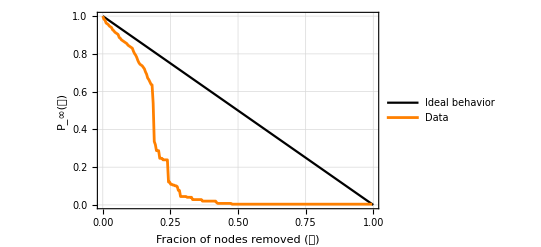

```mathematica
pinfTargeted = {};
totalNodes = VertexCount[g];

tempGraph = geoLocationGraph;
survivorNetworks = {};
Do[
AppendTo[pinfTargeted, {nodeRemovedCount/totalNodes, (Length@Last@Sort@ConnectedComponents@tempGraph)/(totalNodes)}];
maxDegreeNode = Ordering[VertexDegree[tempGraph], -1][[1]];
tempGraph = VertexDelete[tempGraph,VertexList[tempGraph][[maxDegreeNode]]];
AppendTo[survivorNetworks, tempGraph];

, {nodeRemovedCount, 0, totalNodes-1}];
nodeAttackPlot = Show[
Plot[-x + 1,{x, 0,1 }, PlotStyle->{ Black}, PlotTheme->{"Scientific", "FrameGrid"}, PlotLegends->{"Ideal behavior"}, FrameLabel->{"Fracion of nodes removed (𝑓)", "P_∞(𝑓)"}, LabelStyle->{Black, 13}],
ListLinePlot[pinfTargeted, PlotTheme->{"Detailed"}, PlotLegends->{"Data"}, PlotStyle->Orange]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/nodeAttackPlot.pdf",nodeAttackPlot]
```

D:\complex-networks\src\../assets/nodeAttackPlot.pdf

```mathematica
toPlot = survivorNetworks[[50]];

survivorGeoGraphVertex = GeoGraphPlot[toPlot, PerformanceGoal->"Speed", RasterSize->1000, ImageSize->Medium]

survivorCommunities = ConnectedComponents[toPlot];
subgraphs = Subgraph[geoLocationGraph,#]&/@survivorCommunities;
colors = Flatten[{{Red, Cyan, Yellow, Green, Blue}, Table[White, {i, 1, Length@survivorCommunities - 5}]}];
communitiesRainbow = GeoGraphics[
{
{Black, PointSize[.015],Point[#]} &/@ survivorCommunities,
{#1, PointSize[.012],Point[#2]} &@@@ Transpose[{colors, survivorCommunities}]
},
GeoScaleBar->"Metric", RasterSize->1000, GeoProjection->"Orthographic",GeoGridLines->Automatic, GeoBackground->"VectorMonochrome", ImageSize->Large
];

survivorCommunitiesVertexPlot=Rasterize[communitiesRainbow,RasterSize->4000,ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/survivorGeoGraphVertex.pdf",survivorGeoGraphVertex]
Export[NotebookDirectory[]<>"../assets/survivorCommunitiesVertexPlot.pdf",survivorCommunitiesVertexPlot]
```

D:\complex-networks\src\../assets/survivorGeoGraphVertex.pdf

D:\complex-networks\src\../assets/survivorCommunitiesVertexPlot.pdf

### Removing edges

```mathematica
pinfTargeted = {};
(*SetSharedVariable[pinfTargeted] would be cool, but this has to be done sequentially*)
totalNodes = VertexCount[g];
totalEdges = EdgeCount[g];
edgeRemovedCount =0;

survivorNetworksEdge= {};

symm = Normal[Symmetrize@inverseWmat];
tempGraph = AdjacencyGraph[nameIndex, ((If[#>0, 1, 0]&/@#)&/@symm)];

ResourceFunction["MonitorProgress"][
While[edgeRemovedCount < totalEdges,
	AppendTo[pinfTargeted, {edgeRemovedCount/totalEdges, (Length@Last@Sort@ConnectedComponents@tempGraph)/(totalNodes)}];
	AppendTo[survivorNetworksEdge, tempGraph];
	
	max = Max[symm];
	If[max == 0, Break];
	symm=((If[#>=max, 0, #]&/@#)&/@ symm);
	tempGraph = AdjacencyGraph[nameIndex,((If[#>0, 1, 0]&/@#)&/@symm)];
	
	edgeRemovedCount = totalEdges - EdgeCount@tempGraph;

	ResourceFunction["MonitorProgress"]["SetCurrent"][edgeRemovedCount];
	ResourceFunction["MonitorProgress"]["Step"][];

], totalEdges]
;
```

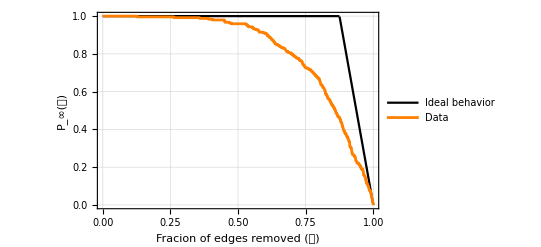

```mathematica
edgeAttackGraph =  Show[
Plot[If[x > .875, -(totalEdges/totalNodes)(x-1),1],{x, 0,1 },PlotStyle->{ Black}, PlotTheme->{"Scientific", "FrameGrid"}, LabelStyle->{Black, 12}, PlotLegends->{"Ideal behavior"}, FrameLabel->{"Fracion of edges removed (𝑓)", "P_∞(𝑓)"}],
ListLinePlot[pinfTargeted~Append~{1, 0} , PlotTheme->{"Detailed"}, PlotLegends->{"Data"}, PlotStyle->Orange]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/edgeAttackGraph.pdf",edgeAttackGraph]
```

D:\complex-networks\src\../assets/edgeAttackGraph.pdf

```mathematica
rules =DeleteDuplicates[#1->GeoPosition[{#5,#6}]&@@@data];
(*This also removes single nodes*)
makeGeo = (network) |->(
(network// EdgeList) /. rules
);

(*This also removes single nodes*)
list = Length[ConnectedComponents[makeGeo[#]]]& /@ survivorNetworksEdge;

listLength = Length@list;
list = {Table[i/listLength, {i, 0, listLength-1}],list} // Transpose;
```

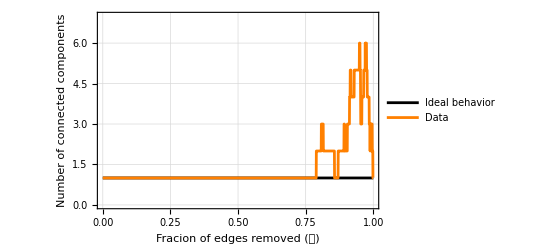

```mathematica
edgeAttackComponentsPlot = Show[
Plot[1, {x, 0, 1}, PlotTheme->{"Detailed"},FrameLabel->{"Fracion of edges removed (𝑓)","Number of connected components"},LabelStyle->{Black,12}, PlotStyle->Black,  PlotRange->{{0, 1}, {0, 7}}, PlotLegends->{"Ideal behavior"}],
ListLinePlot[list, PlotStyle->Orange, PlotLegends->{"Data"}, PlotRange->Full]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/edgeAttackComponentsPlot.pdf",edgeAttackComponentsPlot]
```

D:\complex-networks\src\../assets/edgeAttackComponentsPlot.pdf

```mathematica
survivorCommunities = ConnectedComponents[toPlot];
subgraphs = Subgraph[geoLocationGraph,#]&/@survivorCommunities;
colors = {Red, Green, Blue, Pink, Purple, Cyan, Magenta, Brown, Yellow, White, White}; (*number of colors has to match number of communities*)
communitiesRainbow = GeoGraphics[
{
{Black, PointSize[.015],Point[#]} &/@ survivorCommunities,
{#1, PointSize[.012],Point[#2]} &@@@ Transpose[{colors, survivorCommunities}]
},
GeoScaleBar->"Metric", RasterSize->1000
];

survivorCommunitiesEdgePlot=Rasterize[communitiesRainbow,RasterSize->4000,ImageSize->Medium]
```

# Criteri NP hard che non funzionano

```mathematica
KirchhoffMatrix[g] // Normal // Eigenvalues // Total ;
(%21 / 229) // N
Det[KirchhoffMatrix[g][[2;;,2;;]]] // N
IGSpanningTreeCount[g] // N
IGGlobalEfficiency[g]

GraphResistanceMatrix[g_?GraphQ]:=Module[{kirchhoffMatrix,pseudoInverse,diagonal},kirchhoffMatrix=KirchhoffMatrix[g];
pseudoInverse=PseudoInverse[kirchhoffMatrix];
diagonal=Diagonal[pseudoInverse];
SparseArray[Outer[Plus,diagonal,diagonal]-pseudoInverse-Transpose[pseudoInverse]]]
Omega = GraphResistanceMatrix[g] (*Can't compute*)
```

Node connecrivity and edge connectivity are classical robustness measurements

```mathematica
IGVertexConnectivity[g]
IGEdgeConnectivity[g]
```

229

229

## r energy (Tutta questa cosa è una bullshit totale, impossibile riprodurre i risultati)

```mathematica
ComputeREnergy = (wmat) ↦ (
result = {};
wgraph = WeightedAdjacencyGraph[wmat];
dg = DiagonalMatrix[Power[#, -1/2] &/@ VertexDegree[wgraph]];
AppendTo[result, MatrixPlot[dg]];
symmetricWmat = Rescale@(wmat +Transpose@wmat);
ng = N[IdentityMatrix[VertexCount[wgraph]] - (dg . symmetricWmat . dg)];
AppendTo[result, MatrixPlot[ng]];
gamma = Eigenvalues[ng] // Sort;
AppendTo[result, Variance[gamma]];
AppendTo[result, ListPlot[gamma, PlotRange->Full]];
result
);
```

^^ ez  questa  è  la  r  energy  e  deve  stare  tra  0  e  1

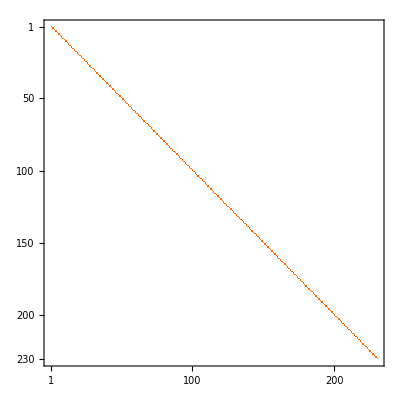
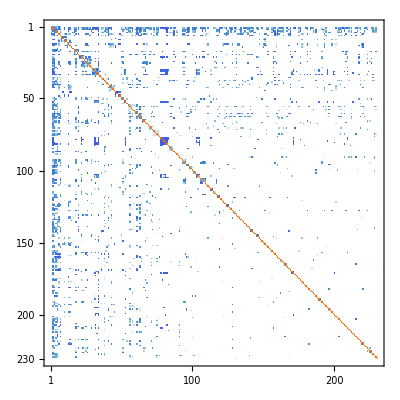
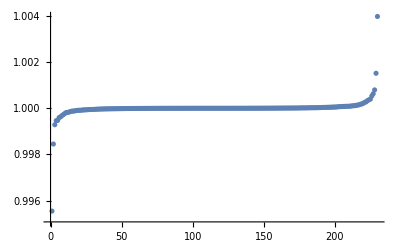
{-Graphics-,-Graphics-,1.93618×10^-7,-Graphics-}

```mathematica
ComputeREnergy[wmat]
```

```mathematica
RandomMatrix = ResourceFunction["RandomMatrix"];
```

```mathematica
wmat2 = RandomMatrix[Real, {0, 10}, 230]
```

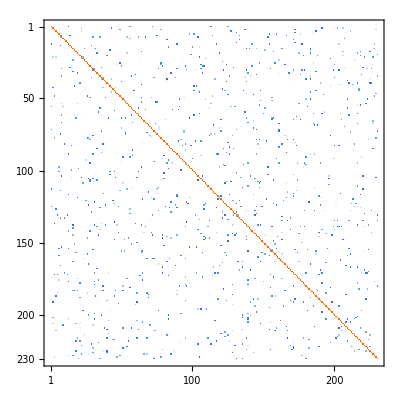
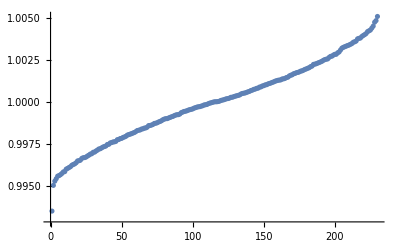
{-Graphics-,-Graphics-,5.76325×10^-6,-Graphics-}

```mathematica
ComputeREnergy[Threshold[wmat2,9.9]]
```